```mathematica
dir=NotebookDirectory[];
```

```mathematica
input=Import[dir<>"../input/"<>"06.txt","Data" ];
```

```mathematica
input
```

{{357,59},{312,283},{130,47},{89,87},{87,58},{158,169},{182,183},{300,318},{82,257},{200,194},{71,259},{112,67},{82,163},{107,302},{58,194},{40,88},{288,339},{64,245},{243,302},{41,43},{147,276},{143,116},{103,178},{262,226},{253,157},{313,71},{202,236},{353,192},{96,74},{167,50},{125,132},{90,315},{174,232},{185,237},{126,134},{152,191},{104,315},{283,90},{95,193},{252,286},{48,166},{69,75},{48,349},{59,124},{334,95},{263,134},{50,314},{196,66},{342,221},{60,217}}

```mathematica
input//Length
```

50

```mathematica
pts=input//SortBy@Last
```

{{41,43},{130,47},{167,50},{87,58},{357,59},{196,66},{112,67},{313,71},{96,74},{69,75},{89,87},{40,88},{283,90},{334,95},{143,116},{59,124},{125,132},{126,134},{263,134},{253,157},{82,163},{48,166},{158,169},{103,178},{182,183},{152,191},{353,192},{95,193},{58,194},{200,194},{60,217},{342,221},{262,226},{174,232},{202,236},{185,237},{64,245},{82,257},{71,259},{147,276},{312,283},{252,286},{107,302},{243,302},{50,314},{90,315},{104,315},{300,318},{288,339},{48,349}}

```mathematica
ptsT={{1,1},{1,6},{8,3},{3,4},{5,5},{8,9}}
```

{{1,1},{1,6},{8,3},{3,4},{5,5},{8,9}}

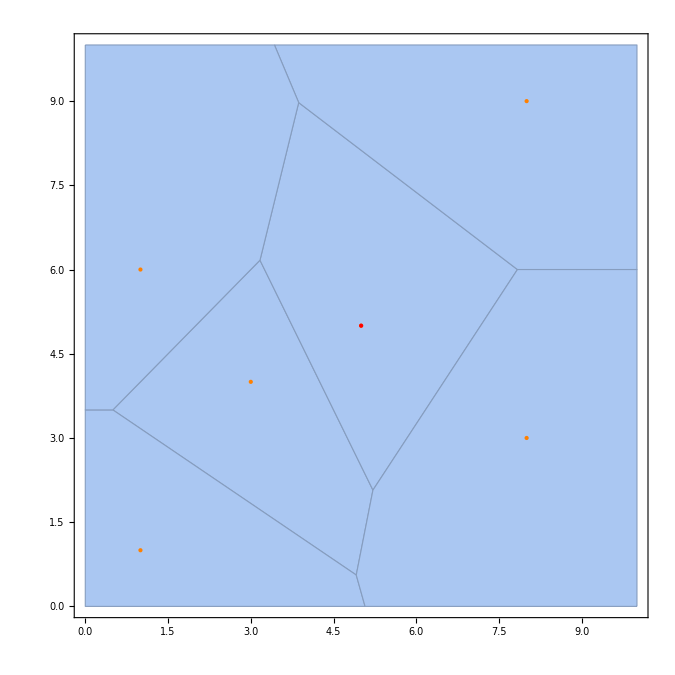

```mathematica
r=Show[VoronoiMesh[ptsT,{{0,10},{0,10}},PlotTheme->"Detailed"],Graphics[{Orange,Point[ptsT]}],Graphics[{PointSize[Large],Red,Point[ptsT[[5]]]}]]
```

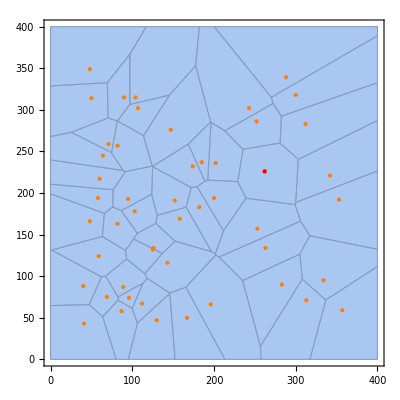

```mathematica
r=Show[VoronoiMesh[pts,{{0,400},{0,400}},PlotTheme->"Detailed"],Graphics[{Orange,Point[pts]}],Graphics[{PointSize[Large],Red,Point[pts[[33]]]}]]
```

```mathematica
IsNearest[i_,{x_,y_},pts_]:=And@@Table[ManhattanDistance[pts[[i]],{x,y}]<ManhattanDistance[pts[[j]],{x,y}],{j,Complement[Range[Length@pts],{i}]}]
```

```mathematica
Near[{x_,y_},pts_]:=Block[{cand},
cand=Select[Range@Length@pts,IsNearest[#,{x,y},pts]&];
If[cand=={},0,cand[[1]]]]
```

```mathematica
sol1T=Table[Near[{i,j},ptsT],{i,0,10},{j,0,10}];sol1T//TableForm
```

1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 2 | 2
1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 2 | 2
1 | 1 | 1 | 4 | 4 | 0 | 2 | 2 | 2 | 2 | 2
1 | 1 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 0 | 0
1 | 1 | 4 | 4 | 4 | 5 | 5 | 5 | 5 | 6 | 6
0 | 0 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 6 | 6
3 | 3 | 3 | 3 | 5 | 5 | 5 | 5 | 6 | 6 | 6
3 | 3 | 3 | 3 | 3 | 5 | 5 | 6 | 6 | 6 | 6
3 | 3 | 3 | 3 | 3 | 3 | 0 | 6 | 6 | 6 | 6
3 | 3 | 3 | 3 | 3 | 3 | 0 | 6 | 6 | 6 | 6
3 | 3 | 3 | 3 | 3 | 3 | 0 | 6 | 6 | 6 | 6

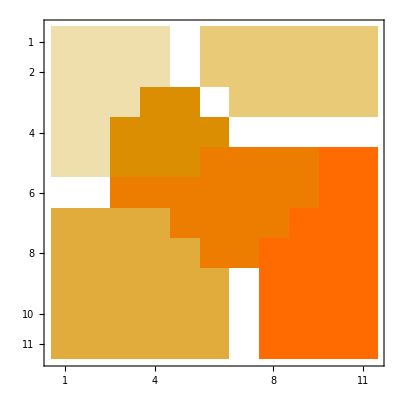

```mathematica
MatrixPlot[sol1T]
```

```mathematica
Border[m_]:=Block[{},
{First@m,Last@m,mᵀ//First,mᵀ//Last}//Flatten//Union
]
```

```mathematica
Border@sol1T
```

{0,1,2,3,6}

```mathematica
sol1T//Function[s,Select[Flatten@s,!MemberQ[Border@s,#]&]]//Tally//SortBy[#,Last]&//Last
```

{5,17}

```mathematica
First/@pts//{Min@#,Max@#}&
```

{40,357}

```mathematica
Last/@pts//{Min@#,Max@#}&
```

{43,349}

```mathematica
sol1=Table[Near[{i,j}],{i,40,360},{j,40,360}];//Timing
```

{2563.59,Null}

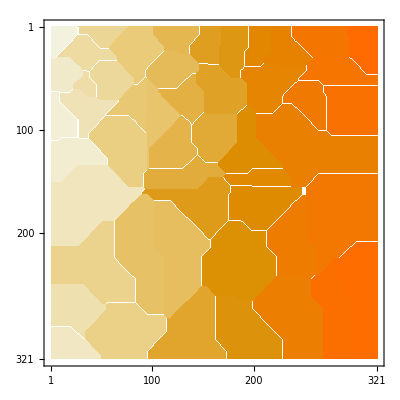

```mathematica
MatrixPlot[sol1]
```

```mathematica
sol1f=sol1//Function[s,Select[Flatten@s,!MemberQ[Border@s,#]&]]//Tally
```

{{10,993},{21,1317},{11,1192},{38,1980},{28,1826},{9,334},{24,1115},{17,962},{18,1244},{43,1261},{7,1253},{34,1861},{26,1729},{15,2617},{23,1564},{25,1518},{36,855},{30,2409},{35,2229},{19,3701},{42,2463},{20,3790},{33,4171}}

```mathematica
sol1f//SortBy[#,Last]&//Last
```

{33,4171}

```mathematica
TotalDist[{x_,y_},pts_]:=Plus@@Table[ManhattanDistance[pts[[i]],{x,y}],{i,Length@pts}]
```

```mathematica
TotalDist[{4,3},ptsT]
```

30

```mathematica
sol2T=Table[TotalDist[{i,j},ptsT],{i,1,10},{j,1,10}];sol2T//TableForm
```

42 | 38 | 34 | 32 | 32 | 34 | 38 | 42 | 46 | 52
40 | 36 | 32 | 30 | 30 | 32 | 36 | 40 | 44 | 50
38 | 34 | 30 | 28 | 28 | 30 | 34 | 38 | 42 | 48
38 | 34 | 30 | 28 | 28 | 30 | 34 | 38 | 42 | 48
38 | 34 | 30 | 28 | 28 | 30 | 34 | 38 | 42 | 48
40 | 36 | 32 | 30 | 30 | 32 | 36 | 40 | 44 | 50
42 | 38 | 34 | 32 | 32 | 34 | 38 | 42 | 46 | 52
44 | 40 | 36 | 34 | 34 | 36 | 40 | 44 | 48 | 54
50 | 46 | 42 | 40 | 40 | 42 | 46 | 50 | 54 | 60
56 | 52 | 48 | 46 | 46 | 48 | 52 | 56 | 60 | 66

```mathematica
sol2T//Select[Flatten@#,#<32&]&//Length
```

16

```mathematica
sol2=Table[TotalDist[{i,j},pts],{i,40,360},{j,40,360}];//Timing
```

{24.0812,Null}

```mathematica
sol2//Select[Flatten@#,#<10000&]&//Length
```

39545